# QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Geometric floquet\\QKT_full.wl"];
```

```mathematica
LaunchKernels[14];
```

```mathematica
Names["QKT`*"]
```

{ClassicalMapeo,ClassicalStep,ClassicalToDisk,ClassicalToSphere,COEAsymptoticSigma2,COESFFAnalytical,CompileLevelCounter,CompileSFF,ComputeSigma2Sliding,EnsembleSFF,EnsembleSigma2,EvaluateSpectrumSigma2,Floq,Floqb,Floqbn,Floqn,Floqsym,FluctuationPowerSpectrum,GenerateCOEEnsemble,generateCoherentStateCompiler,GenerateQKTEnsemble,generateSpinOperators,GetFluctuations,GetQKTParityEigensystem,GetQKTParitySpectra,IntWignerCOE,IPR,LengthSpectrum,MeanLevelSpacingRatio,NNSpacings,ParitySectorIndices,PoolSpacingRatios,PoolSpacings,PrCOE,PrCUE,PrPoisson,RandomCOESpectrum,SingleSFF,SingleSpectrumSigma2,UnfoldLinear,ValidateUnfolding,WignerCOE}

```mathematica
Clear[SplitQKTParity];
SplitQKTParity[Op_?MatrixQ]:=Module[{dim,Jval,OpEven,OpOdd},
(*Calculate J from the dimension of the matrix (dim=2J+1)*)
dim=Length[Op];
Jval=(dim-1)/2;
If[EvenQ[Jval],
(*If J is EVEN:Row 1 (M=J) is Even Parity*)
OpEven=Op[[1;; ;;2,1;; ;;2]];
OpOdd=Op[[2;; ;;2,2;; ;;2]];,
(*If J is ODD:Row 1 (M=J) is Odd Parity*)
OpEven=Op[[2;; ;;2,2;; ;;2]];
OpOdd=Op[[1;; ;;2,1;; ;;2]];];
{OpEven,OpOdd}];
```

## QKT

```mathematica
(*Floquet parameters*)
J=207;
α=0.84;
k=1.3;
```

```mathematica
(*Generates all J operators, Jx, Jy, Jz, Jx^2*)
ops=generateSpinOperators[J];
```

```mathematica
?GetQKTParityEigensystem
```

```mathematica
data=GetQKTParityEigensystem[J,α,k];
```

```mathematica
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.394154,0.374073}

```mathematica
(*Unfolding, only works for uniform density of states in the chaotic regime COE*)
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

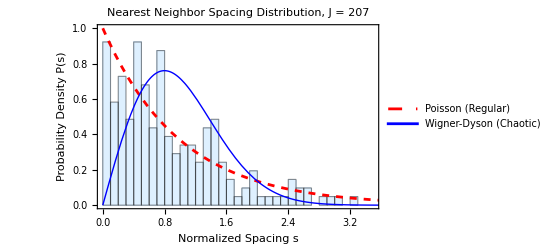

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

```mathematica
(*Unfolding, only works for uniform density of states in the chaotic regime COE*)
phases=Sort[Arg[eigenvalm]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

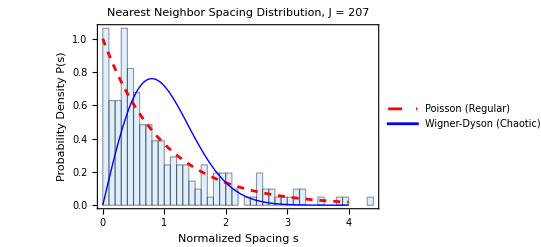

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

## IPR & Husimis

```mathematica
(*Resolution of the grid for the phase space*)
radius=2;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31397,2}

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31397 points...

```mathematica
ops=generateSpinOperators[J];
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] :=Uk[ k]. U0[α];
Clear[V];
V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];
```

```mathematica
data=GetQKTParityEigensystem[J,α,k];
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{eigenvecM,eigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};
```

```mathematica
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
Vop=V[α,k];
```

```mathematica
(*Sorting with respect the average energy*)
ae=Chop[Map[#.Vop.ConjugateTranspose[#]&,neweigenvec]];
```

```mathematica
ordering=Ordering[ae];
(*Sort eigenvectors and expectations accordingly*)
eigenvecsSorted=neweigenvec[[ordering]];
eigenvalSorted=neweigenval[[ordering]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>" (kick-rotation)",25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,Background->White]
```

-Graphics-

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiValuesSorted=husimiValues;
```

```mathematica
(*Set parameters, 2J+1 Husimis in total*)
numEigenstates=2J+1; 
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListContourPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["AE Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"AE_Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];
plot],{q,numEigenstates}];
```

## LDoS

```mathematica
(*Floquet parameters*)
J=207;
α=0.84;
k=1.3;
```

```mathematica
ops=generateSpinOperators[J];
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] :=Uk[ k]. U0[α];
Clear[V];
V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];
```

```mathematica
data=GetQKTParityEigensystem[J,α,k];
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{eigenvecM,eigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};
```

```mathematica
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
selectedpoints={{Rationalize[0.5],Rationalize[0.]},{Rationalize[0.5],Rationalize[1.]},{Rationalize[0.84],Rationalize[1.1]},{Rationalize[1.65],Rationalize[0.7]},{Rationalize[0.70],Rationalize[1.075]}};
```

```mathematica
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,selectedpoints,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

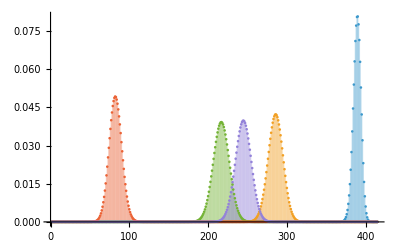

```mathematica
ListPlot[Abs[statesCompiled]^2,Filling->Bottom,PlotRange->All]
```

```mathematica
coherentfloq=ParallelTable[Conjugate[neweigenvec].i,{i,statesCompiled}];
```

```mathematica
dos=Table[Transpose[{Arg[neweigenval],Abs[i]^2}],{i,coherentfloq}];
```

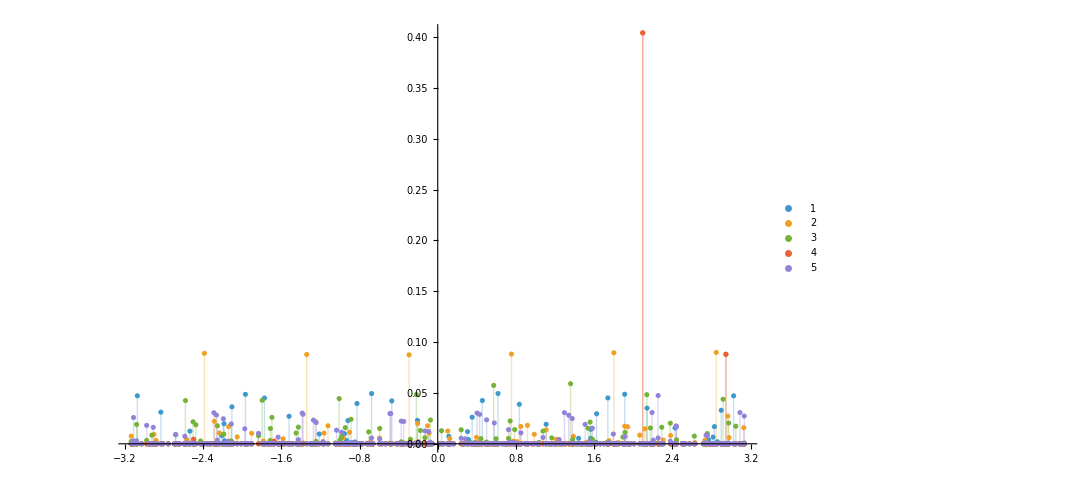

```mathematica
ListPlot[dos,PlotRange->All,Filling->Bottom,PlotLegends->Automatic,ImageSize->800]
```

```mathematica
(*Vop=ops[[3]]; *)
Vop=V[α,k];
(*1. Calculate the real expectation value ⟨ψ|V|ψ⟩*)
ae=(1/J)Chop[Map[Conjugate[#].Vop.#&,neweigenvec]];
(*2. Get the permutation array that sorts from lowest to highest expectation value*)
ordering=Ordering[ae];
(*3. Sort both the eigenvectors and eigenvalues perfectly in sync*)
eigenvecsSorted=neweigenvec[[ordering]];
eigenvalSorted=neweigenval[[ordering]];
```

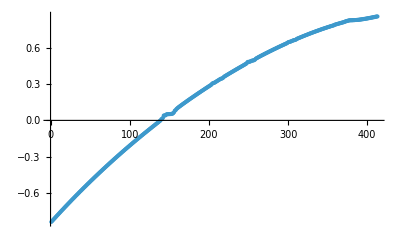

```mathematica
ListPlot[Sort[ae],PlotRange->All]
```

```mathematica
coherentfloq=ParallelTable[Conjugate[eigenvecsSorted].i,{i,statesCompiled}];
```

```mathematica
sorteddos=Table[Transpose[{Sort[ae],Abs[i]^2}],{i,coherentfloq}];
```

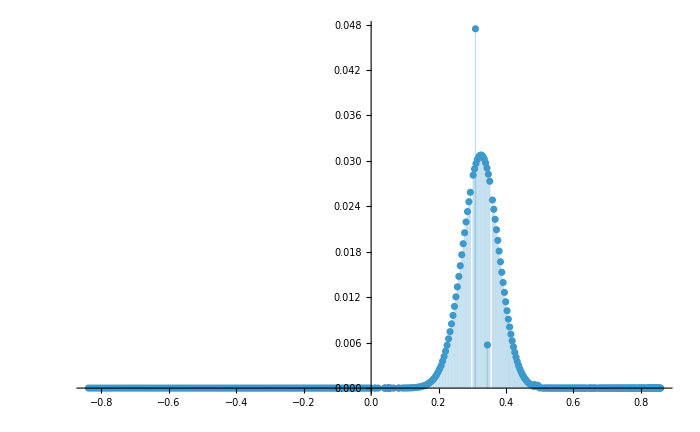

```mathematica
ListPlot[sorteddos[[5]],Filling->Bottom,ImageSize->700,PlotRange->All]
```

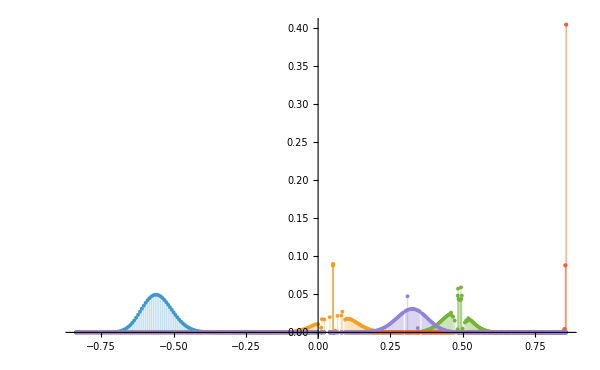

```mathematica
ListPlot[sorteddos,Filling->Bottom,ImageSize->600,PlotRange->All]
```

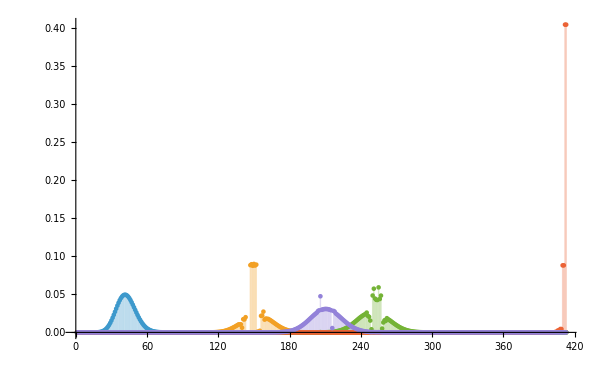

```mathematica
ListPlot[Table[Abs[i]^2,{i,coherentfloq}],Filling->Bottom,ImageSize->600,PlotRange->All]
```

## Scaling

```mathematica
selectedpoints={{Rationalize[0.5],Rationalize[1.]},{Rationalize[0.84],Rationalize[1.1]},{Rationalize[1.65],Rationalize[0.7]},{Rationalize[0.70],Rationalize[1.075]},{Rationalize[0.75],Rationalize[1]}};
```

```mathematica
ClearAll[ipr];
(*Highly optimized IPR for a matrix of states*)
ipr[matrix_]:=Total[Abs[matrix]^4,{2}];
(*Floquet parameters*)
α=0.84;
k=1.3;
(*2. Compile the generator ONCE outside the loop*)
coherentStateGenerator=generateCoherentStateCompiler[];
```

```mathematica
(*3. DISTRIBUTE DEFINITIONS to all parallel CPU cores*)
(*You must list every custom function and variable the loop needs to see*)
DistributeDefinitions[GetQKTParityEigensystem,ipr,coherentStateGenerator,selectedpoints,α,k];
```

```mathematica
Print["Starting Parallel Evaluation on ",$KernelCount," cores..."];
AbsoluteTiming[(*4. The Parallel Outer Loop*)
alldata=ParallelTable[
data=GetQKTParityEigensystem[J,α,k];
neweigenvec=Riffle[data["Even","FullVectors"],data["Odd","FullVectors"]];
statesCompiled=Map[coherentStateGenerator[J,#[[1]],#[[2]]]&,selectedpoints];
coherentfloq=Transpose[Conjugate[neweigenvec].Transpose[statesCompiled]];
info=ipr[coherentfloq];
{J,info}
,{J,50,500}];]
Print["Done!"];
```

Starting Parallel Evaluation on 14 cores...

{264.413,Null}

Done!

```mathematica
(*0. CRITICAL:Force the data to be strictly ordered by J (the first column)*)
alldata=SortBy[alldata,First];
(*1. Extract the J values (the x-axis)*)
jValues=alldata[[All,1]];
(*2. Extract and separate the IPR data for all 4 states*)
iprValues=Transpose[alldata[[All,2]]];
(*3. Pair the J values with their respective IPR lists*)
linesToPlotp=Table[Transpose[{jValues,iprValues[[i]]}],{i,Length[iprValues]}];
```

```mathematica
Export["with_parallelization.m",linesToPlotp];
```

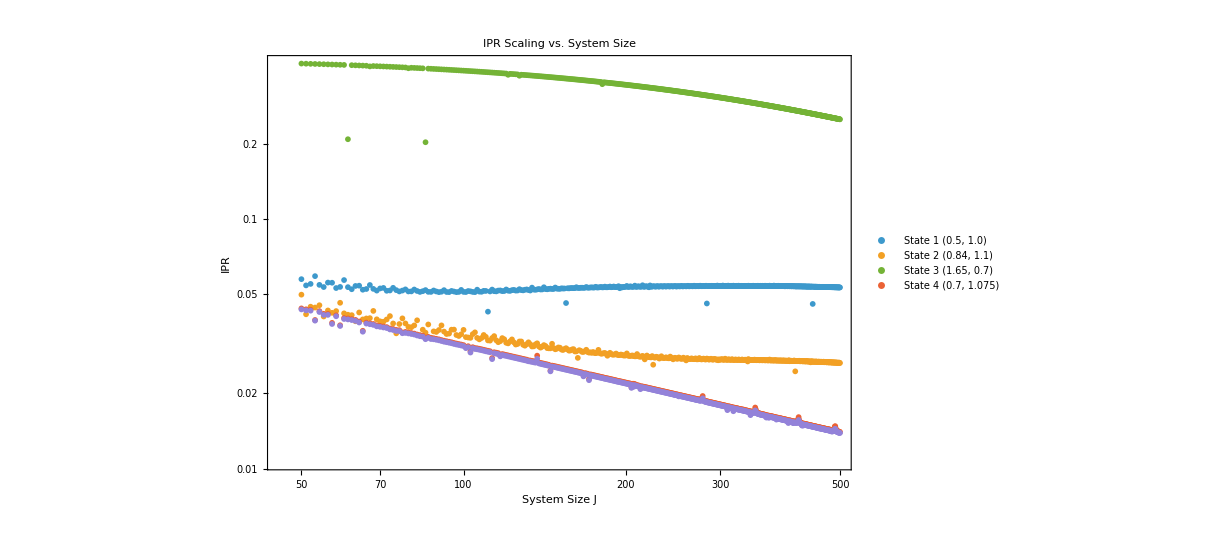

```mathematica
(*4. Plot on a Log-Log scale to reveal the scaling exponents*)
ListLogLogPlot[linesToPlotp,Joined->False,Mesh->All,PlotRange->All,PlotStyle->Thickness[0.005],PlotLegends->Placed[LineLegend[{"State 1 (0.5, 1.0)","State 2 (0.84, 1.1)","State 3 (1.65, 0.7)","State 4 (0.7, 1.075)"}],Right],Frame->True,FrameLabel->{"System Size J","IPR"},PlotLabel->"IPR Scaling vs. System Size",BaseStyle->{FontFamily->"Helvetica",FontSize->14},ImageSize->900]
```

## Scaling by parity

```mathematica
Print["Starting Parallel Evaluation on ",$KernelCount," cores..."];
AbsoluteTiming[
(*4. The Parallel Outer Loop*)
alldata=ParallelTable[data=GetQKTParityEigensystem[J,α,k];
(*Grab the sectors separately WITHOUT Riffle*)
vecEven=data["Even","FullVectors"];
vecOdd=data["Odd","FullVectors"];
(*Generate the states*)
statesCompiled=Map[coherentStateGenerator[J,#[[1]],#[[2]]]&,selectedpoints];
(*Two distinct BLAS matrix multiplications*)
overlapsEven=Transpose[Conjugate[vecEven].Transpose[statesCompiled]];
overlapsOdd=Transpose[Conjugate[vecOdd].Transpose[statesCompiled]];
(*Calculate IPR for both sectors*)infoEven=ipr[overlapsEven];
infoOdd=ipr[overlapsOdd];
(*Store as {J,{Even IPRs},{Odd IPRs}}*){J,infoEven,infoOdd},{J,100,300}];]
Print["Done!"];
```

Starting Parallel Evaluation on 14 cores...

{25.7016,Null}

Done!

```mathematica
(*0. CRITICAL:Force the data to be strictly ordered by J*)
alldata=SortBy[alldata,First];
(*1. Extract the J values (the x-axis)*)
jValues=alldata[[All,1]];
(*2. Extract and separate the IPR data for Even and Odd*)
iprValuesEven=Transpose[alldata[[All,2]]];
iprValuesOdd=Transpose[alldata[[All,3]]];
(*3. Pair the J values with their respective IPR lists*)
linesEven=Table[Transpose[{jValues,iprValuesEven[[i]]}],{i,Length[iprValuesEven]}];
linesOdd=Table[Transpose[{jValues,iprValuesOdd[[i]]}],{i,Length[iprValuesOdd]}];
(*Join them into a single list of 8 lines (4 Even,followed by 4 Odd)*)
linesToPlotp=Join[linesEven,linesOdd];
Export["with_parallelization_parity.m",linesToPlotp];
```

```mathematica
(*1. Dynamically determine the number of states to prevent indexing errors*)
numStates=Length[selectedpoints];
(*2. Generate a list of individual plots*)
individualPlots=Table[ListLogLogPlot[(*Correctly pair the Even state with its exact Odd counterpart*)
{linesToPlotp[[i]],linesToPlotp[[i+numStates]]},Joined->True,Mesh->All,PlotRange->All,(*Keep the color consistent,solid for Even,dashed for Odd*)PlotStyle->{Directive[ColorData[97][i],AbsoluteThickness[2]],Directive[ColorData[97][i],Dashed,AbsoluteThickness[2]]},PlotLegends->Placed[LineLegend[{"State "<>ToString[i]<>" (Even)","State "<>ToString[i]<>" (Odd)"}],Right],Frame->True,FrameLabel->{"System Size J","IPR"},PlotLabel->"State "<>ToString[i]<>" Scaling (Even vs. Odd)",BaseStyle->{FontFamily->"Helvetica",FontSize->14},ImageSize->1000],{i,1,numStates} (*Loop exactly over the number of states you computed*)];
```

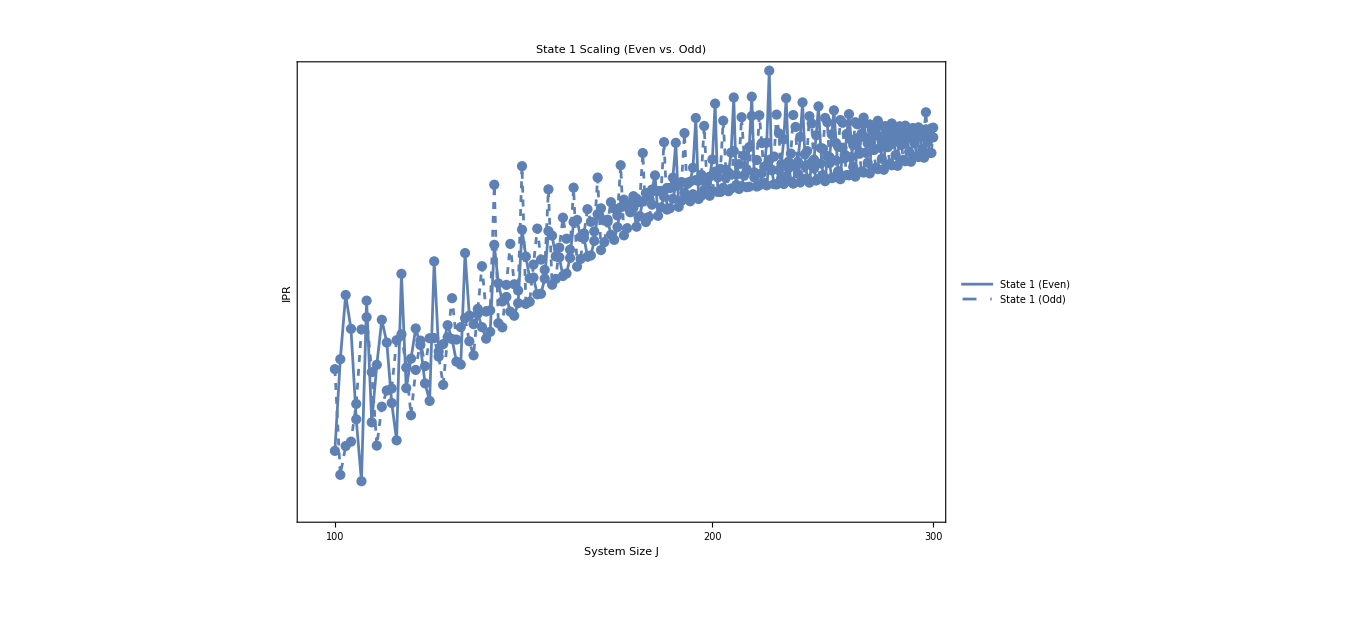
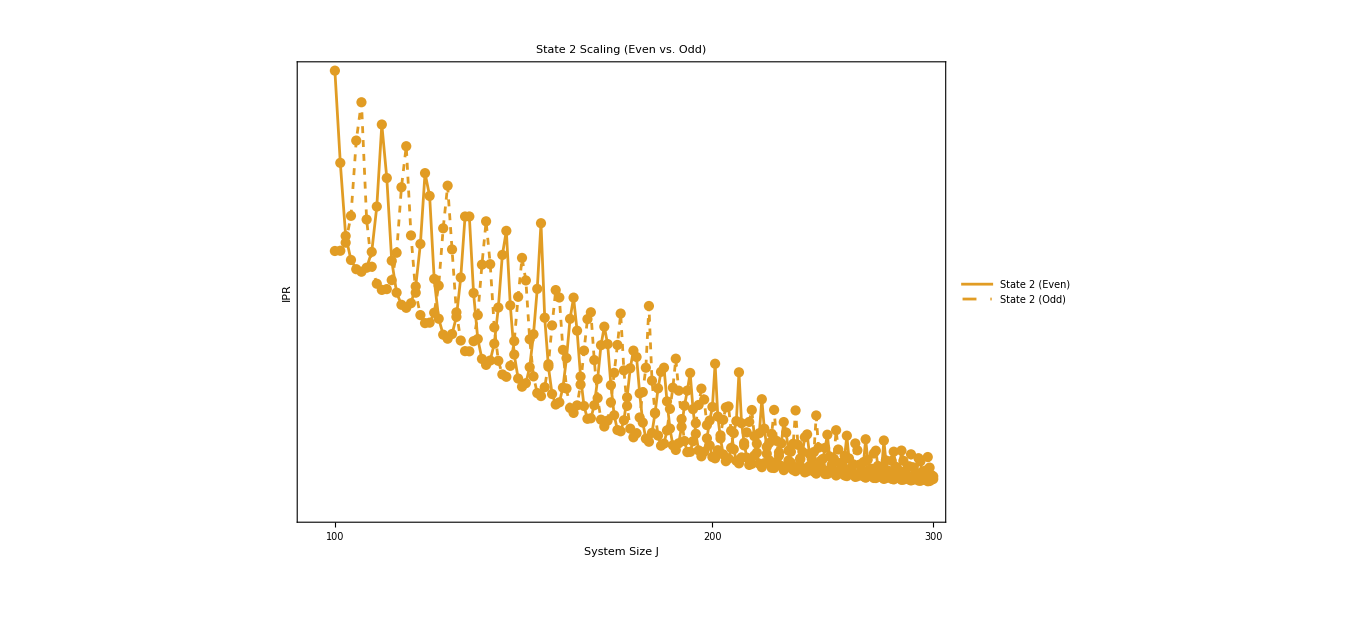
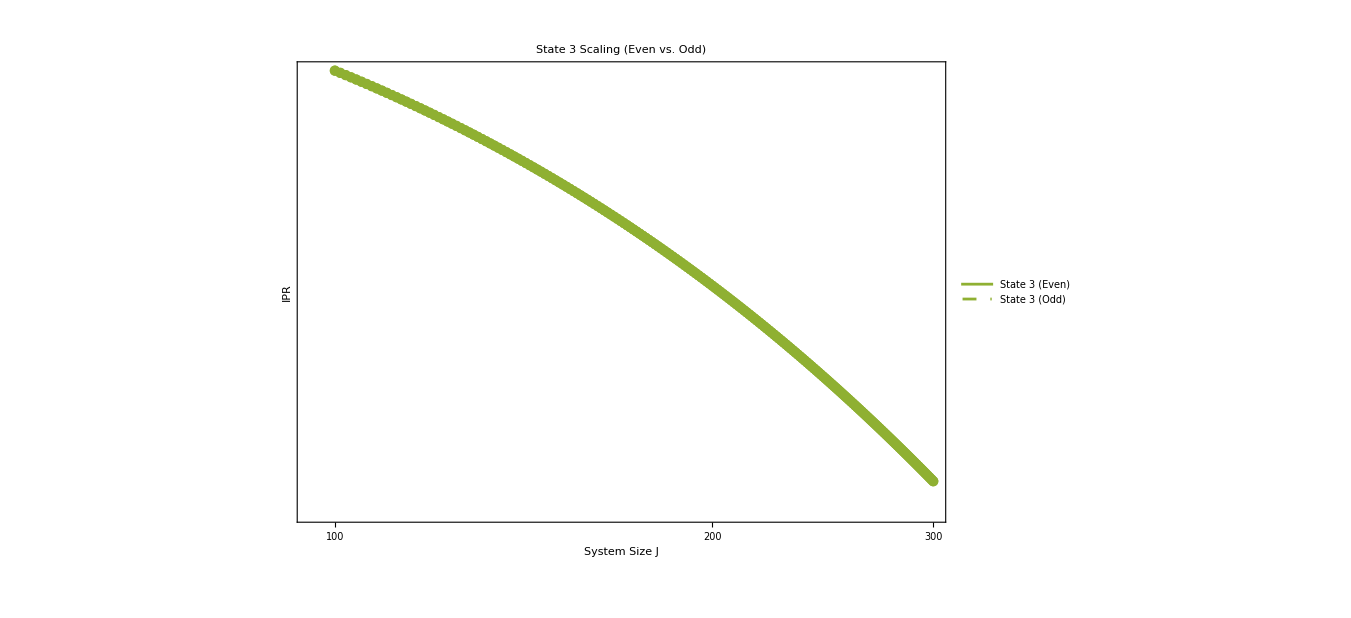
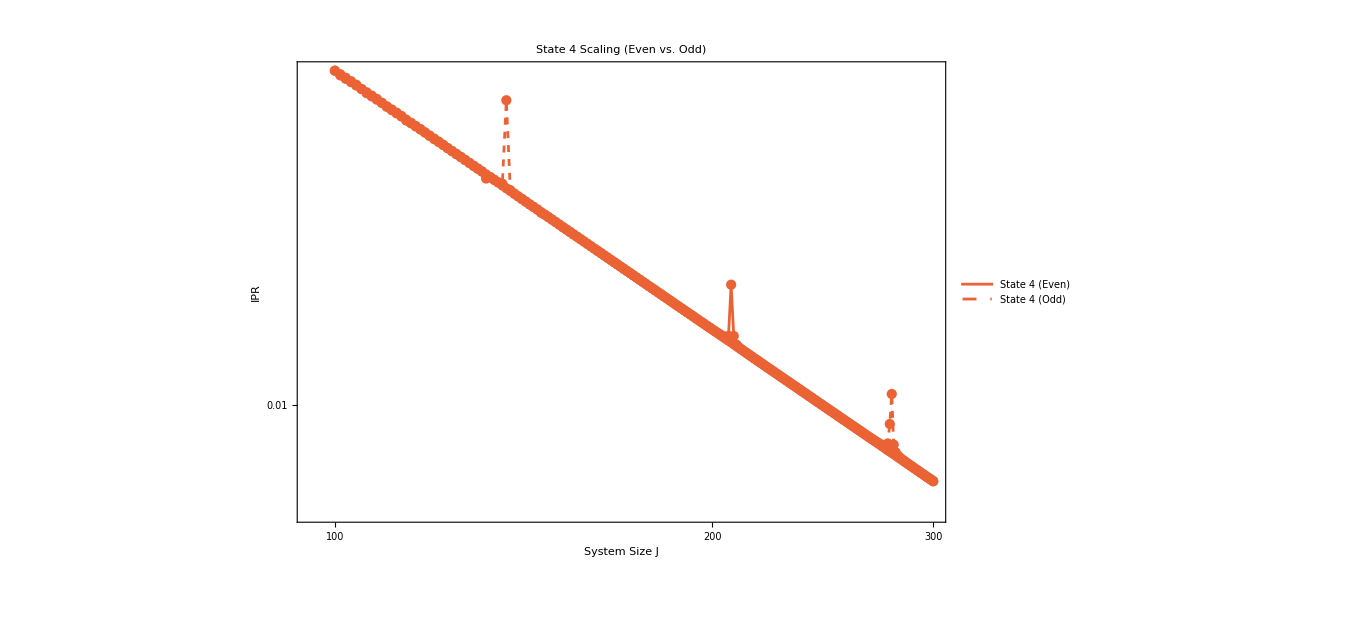
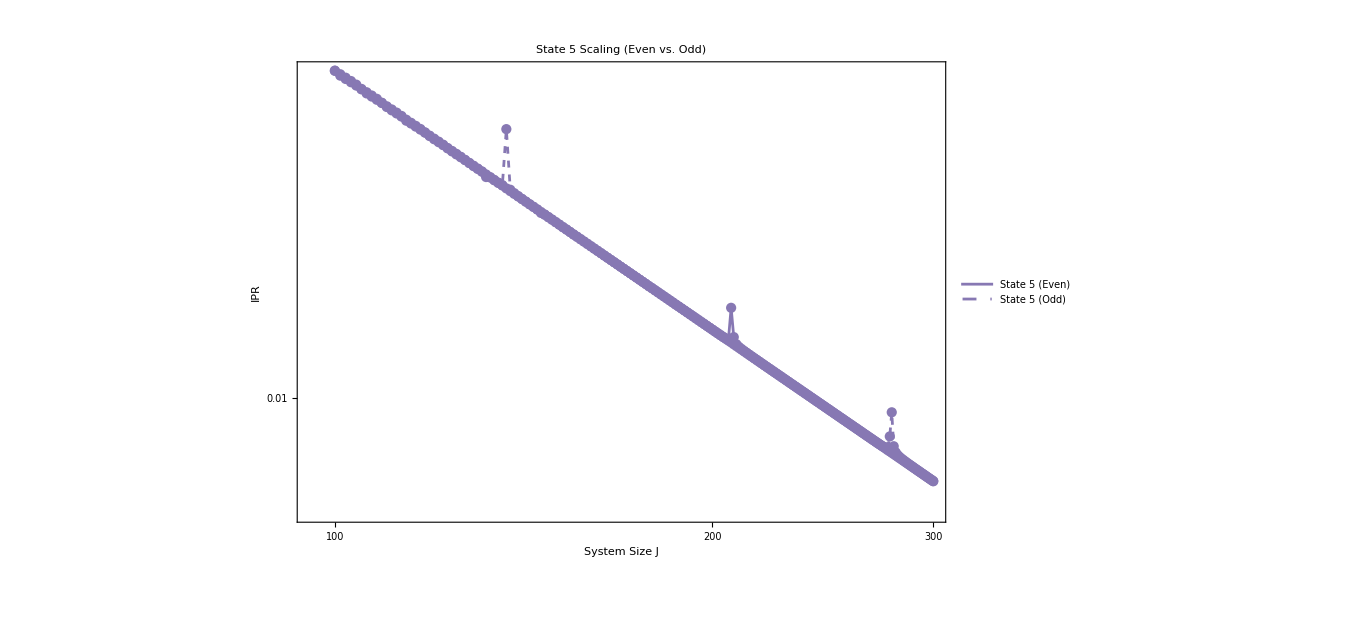

```mathematica
individualPlots
```

# Average energy

## Average energy

```mathematica
(*Floquet parameters*)
J=2000;
α=0.84;
k=1.3;
```

```mathematica
ops=generateSpinOperators[J];
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] :=Uk[ k]. U0[α];
Clear[V];
V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];
```

```mathematica
data=GetQKTParityEigensystem[J,α,k];
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{eigenvecM,eigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};
```

```mathematica
Vop=V[α,k];
{szM,szm}=SplitQKTParity[V[α,k]];
szExpectationsM=(1/J)Map[#.szM.ConjugateTranspose[#]&,eigenvecM];
szExpectationsm=(1/J)Map[#.szm.ConjugateTranspose[#]&,eigenvecm];
```

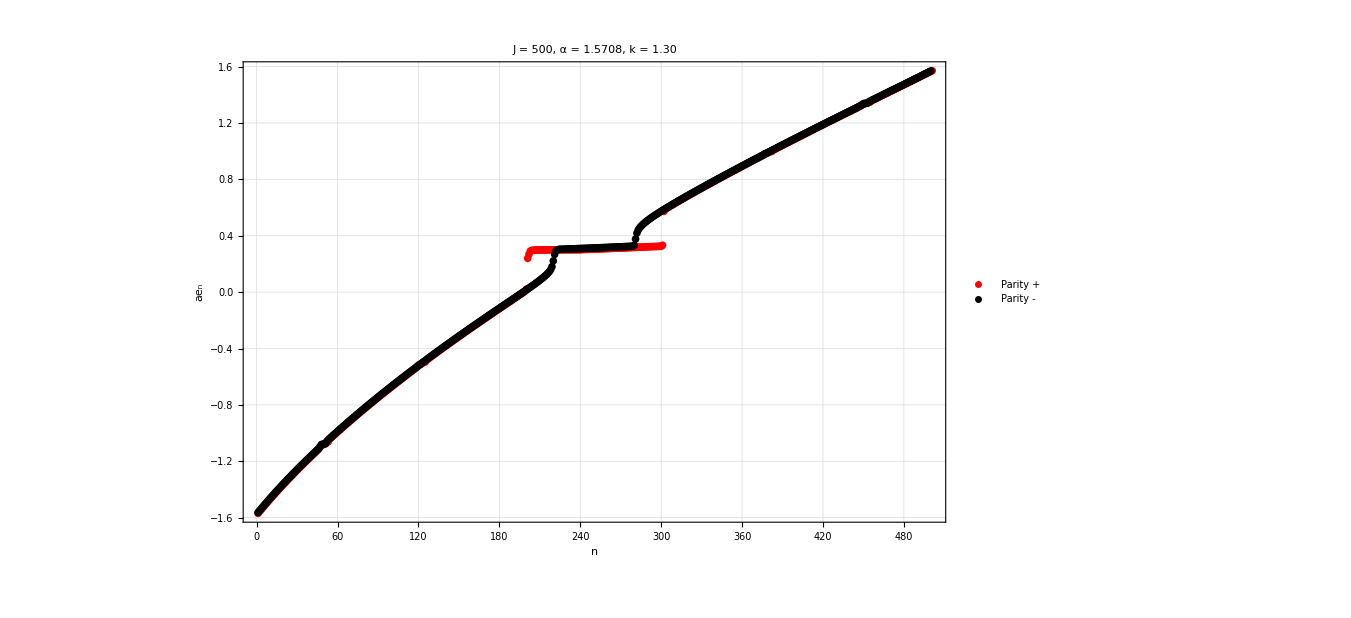

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000]
```

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
```

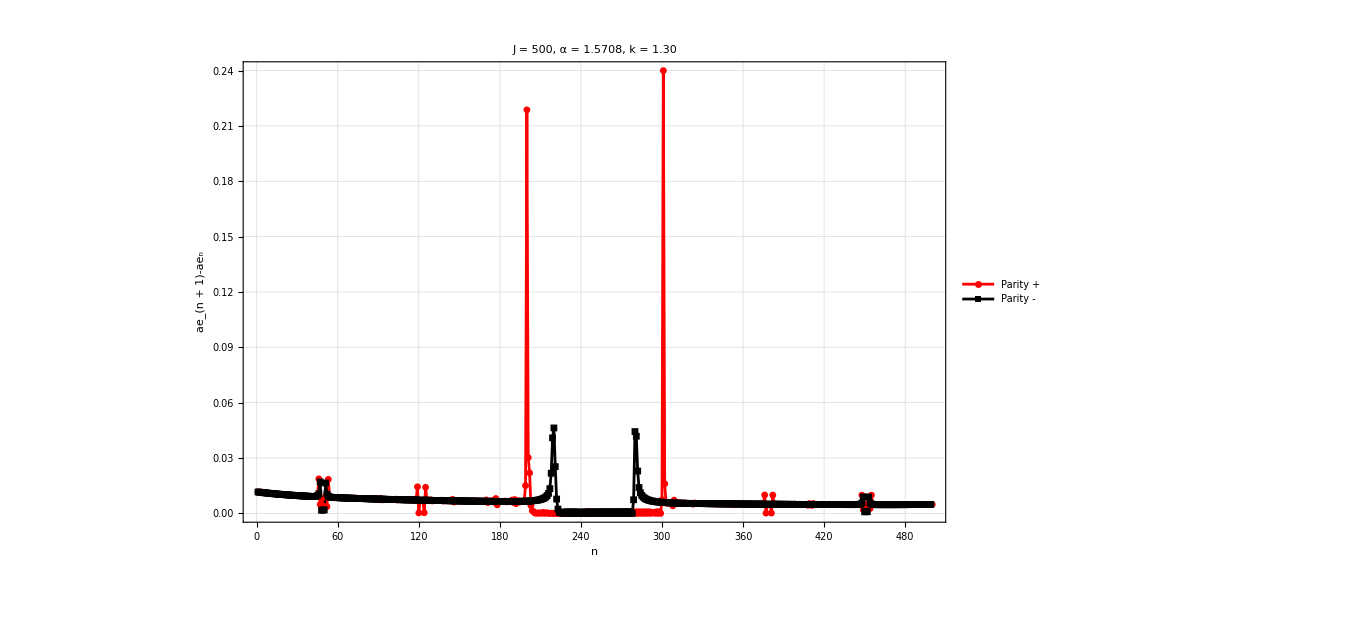

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->1000]
```

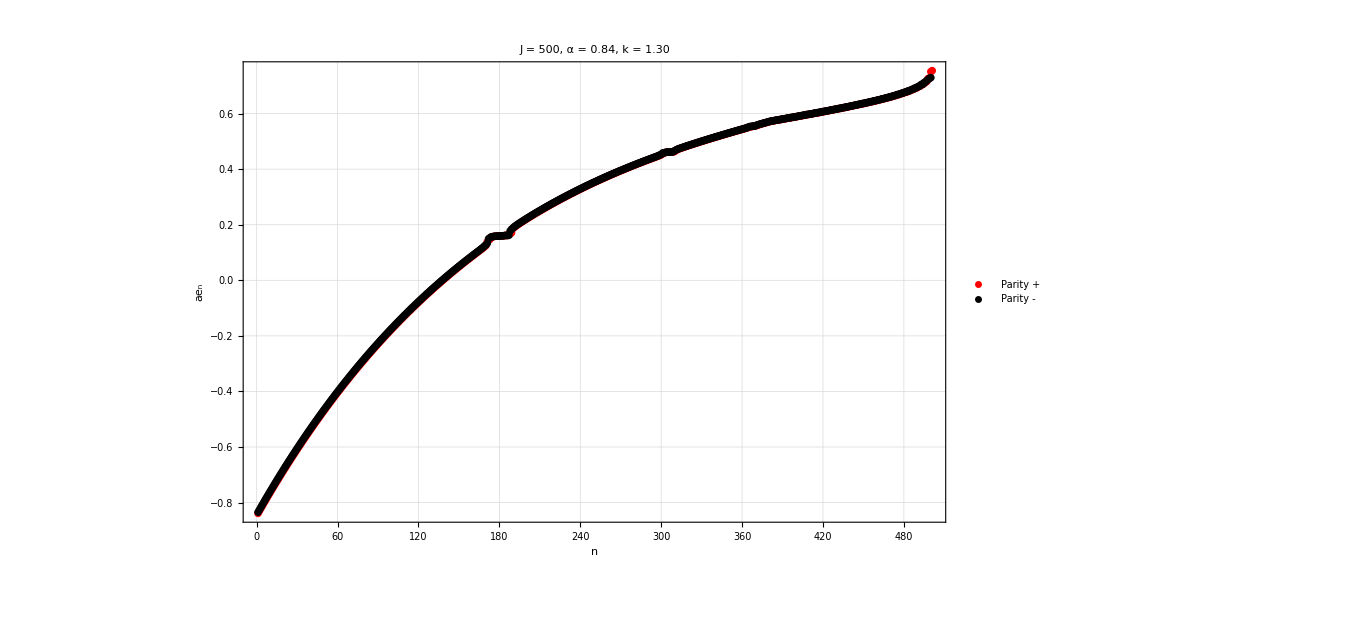

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000]
```

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
```

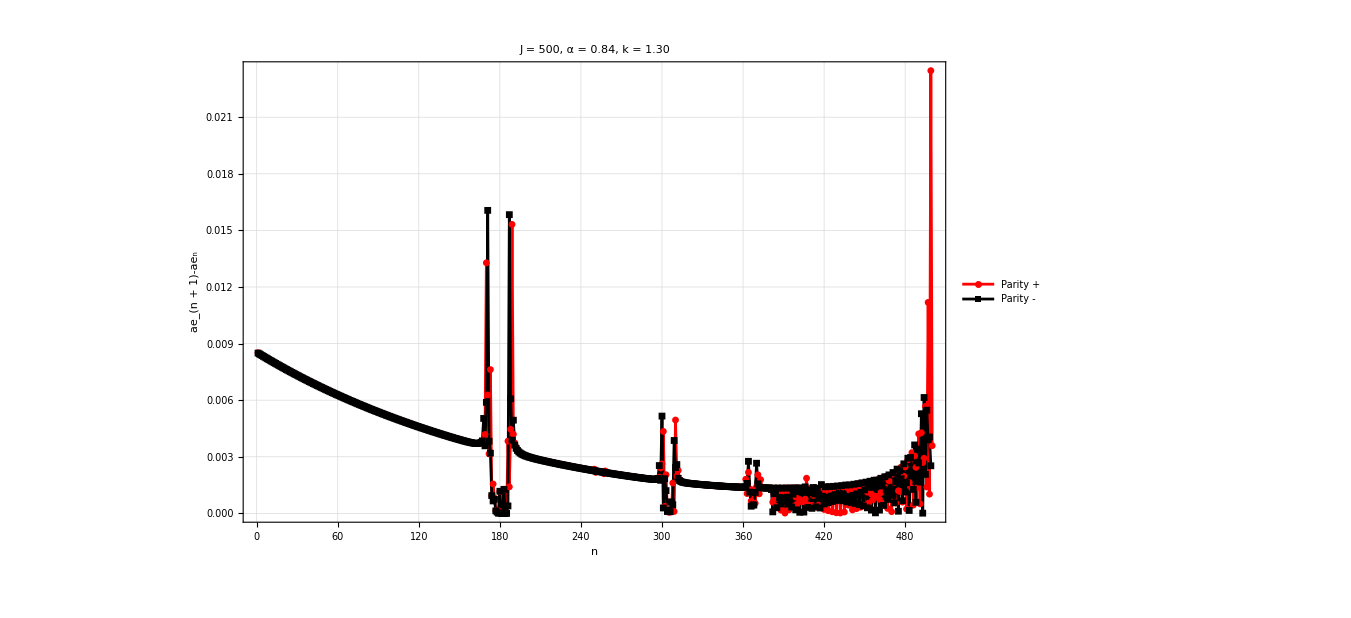

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->1000]
```

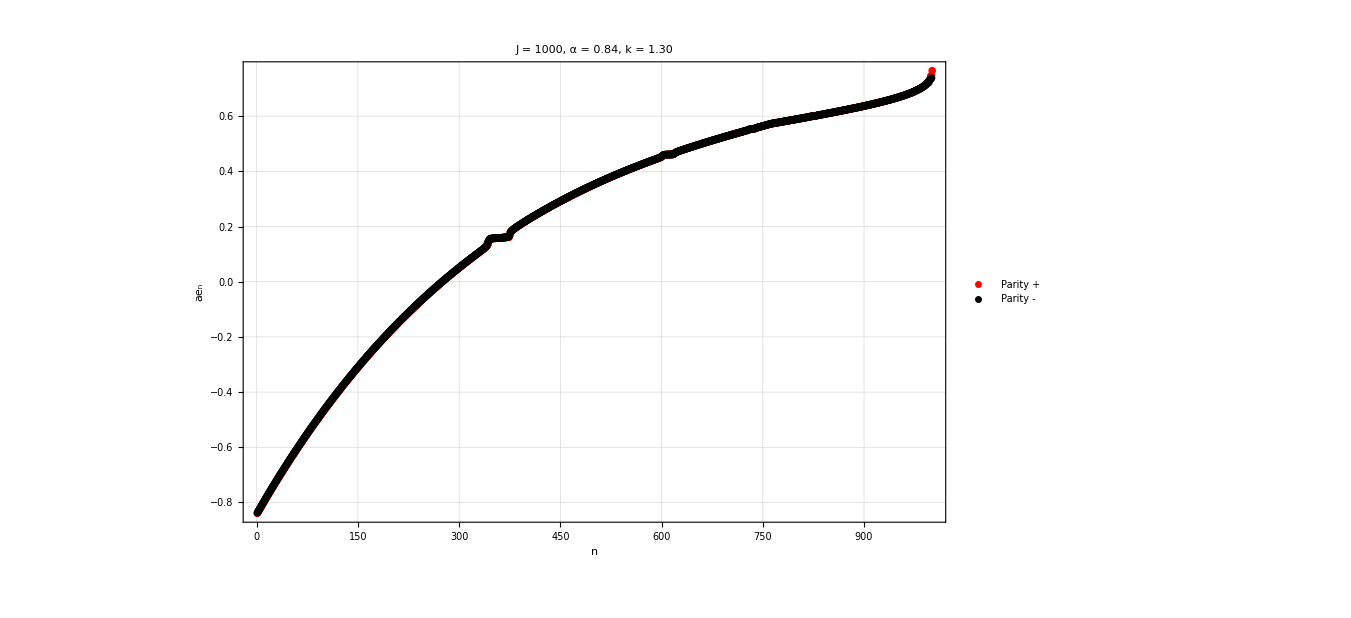

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000]
```

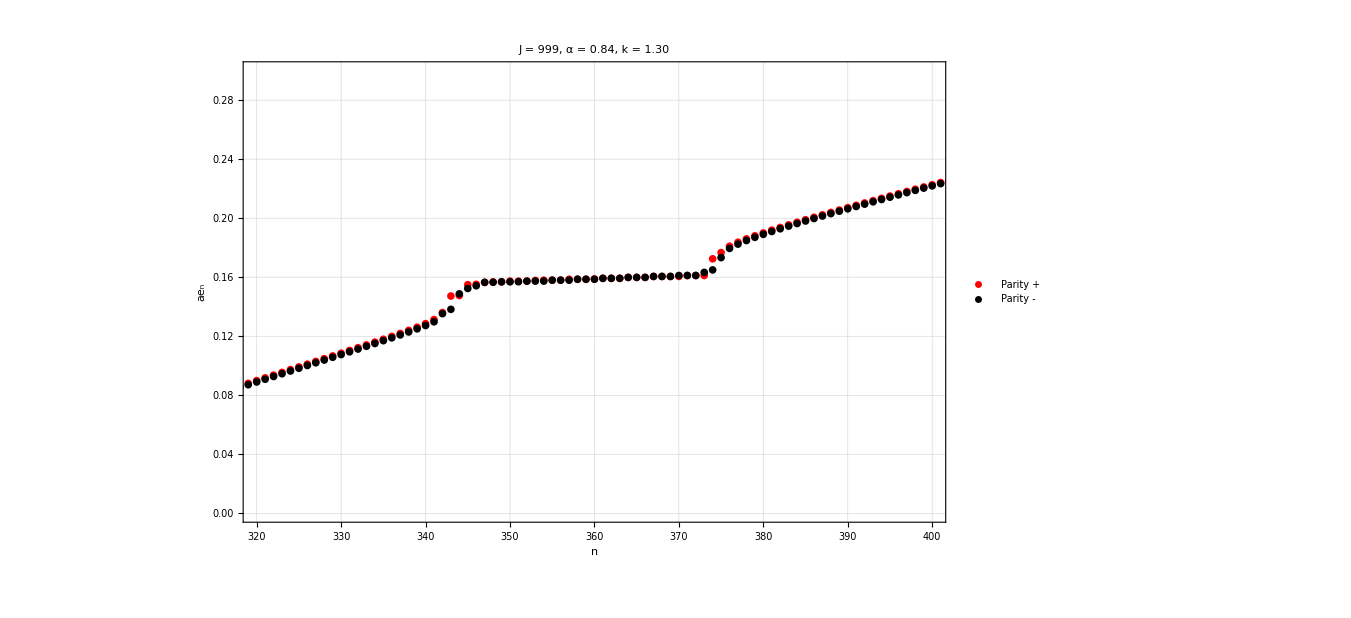

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000,PlotRange->{{320,400},{0,0.3}}]
```

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
```

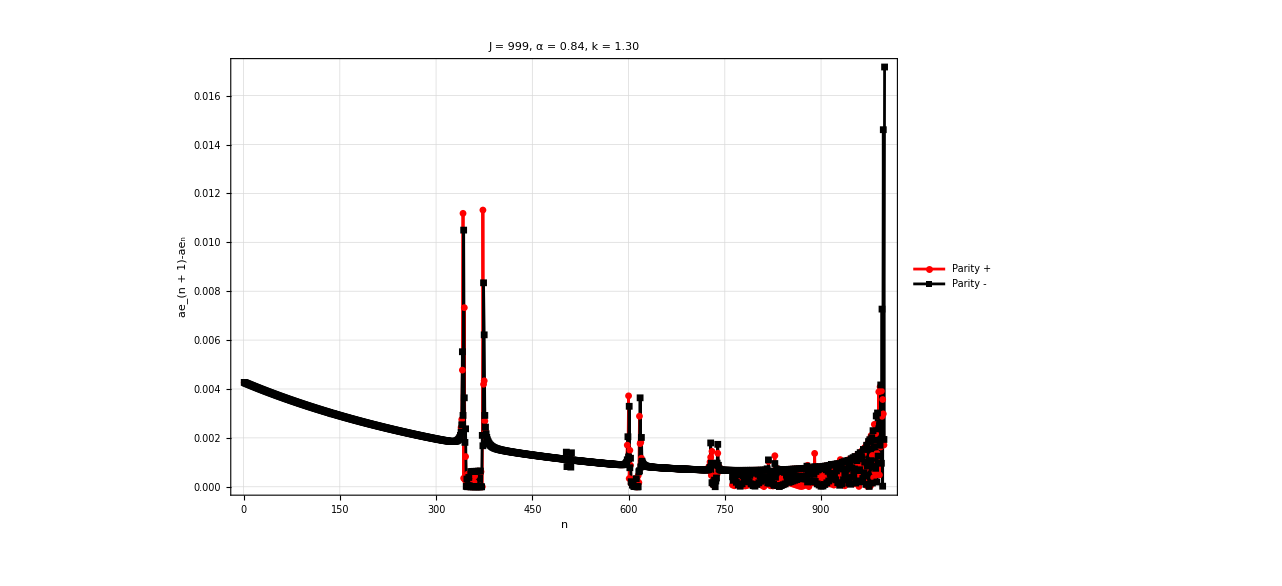

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->1000]
```

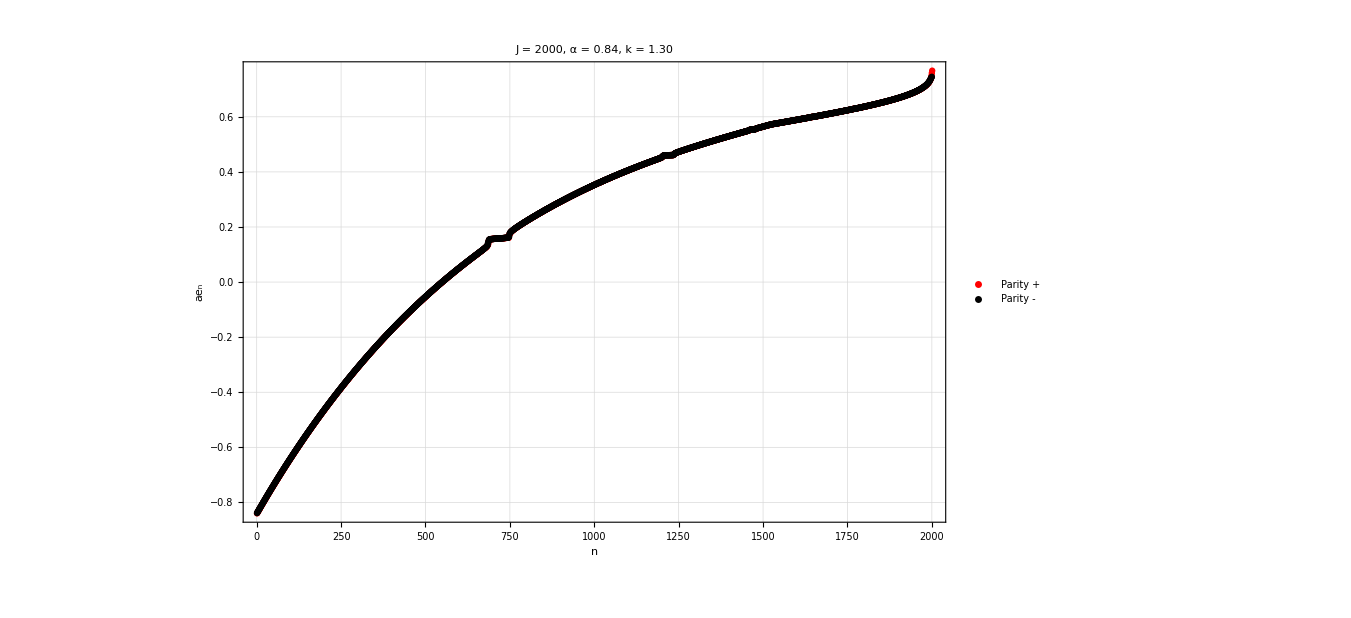

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000]
```

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
```

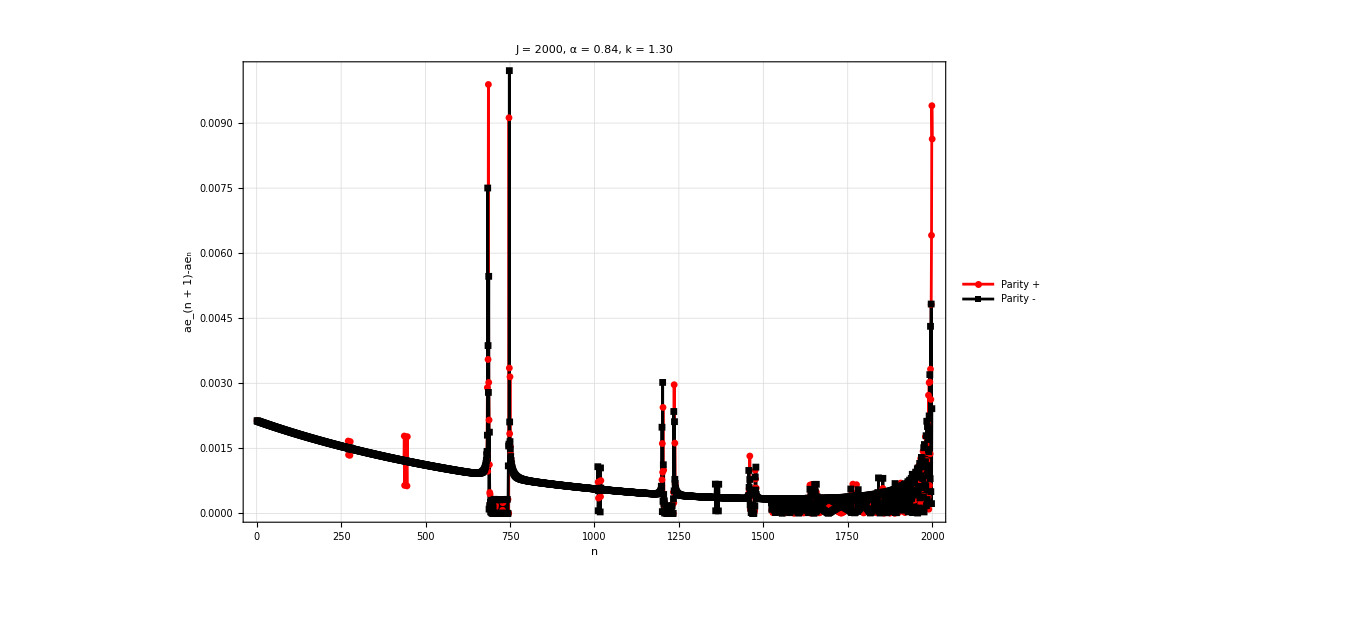

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->1000]
```

## Average density of states

```mathematica
(*Floquet parameters*)
J=1000;
α=0.84;
```

```mathematica
k=1.3;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] := U0[α].Uk[ k];
```

```mathematica
Clear[V];
V[α_,k_]:=(k/(2J))ops[[4]]+α*ConjugateTranspose[Uk[k]].ops[[3]].Uk[k];
```

```mathematica
Vop=V[α,k];
```

```mathematica
Clear[mat];
Print["Computing matrix by parity sector..."];
mat=Vop;
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing matrix by parity sector...

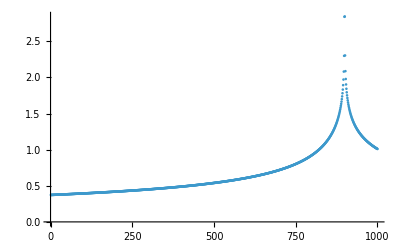

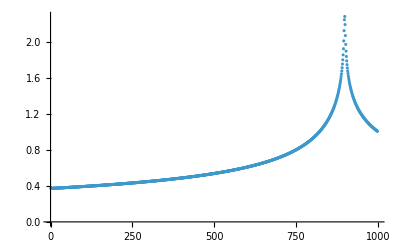

```mathematica
ListPlot[1/Differences[Sort[Chop[eigenvalM]]],PlotRange->All]
ListPlot[1/Differences[Sort[Chop[eigenvalm]]],PlotRange->All]
```

# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Geometric floquet\\QKT_full.wl"];
```

```mathematica
LaunchKernels[14];
```

## Computations

```mathematica
(*Execution*)
α=Pi/2.;
k=1.3;
kicks=2000;
(*Random inintial conditions on the disk/phase space*)
points=150;
randomregion=RandomPoint[Disk[{0,0},1.9999],points];
```

```mathematica
(*The'Listable' attribute handles the parallel iteration over'randomregion' automatically*)
result=ClassicalMapeo[randomregion,α,k,kicks,1];
```

```mathematica
newpoincarea=ArrayReshape[result,{points*kicks,2}];
plot=ListPlot[newpoincarea,PlotStyle->Directive[PointSize[0.0002],Opacity[0.18],Black],PlotLabel->Row[{Style["α = ",35,Black],Style[N[α],35,Black],Style[", k = ",35,Black], Style[N[k],35,Black],Style[" (kick-rotation)",24,Black]}],FrameLabel->{Style["Q",30,Black],Rotate[Style["P",30,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,PlotRange->{{-2,2},{-2,2}},GridLines->{Range[-2,2,0.2], Range[-2,2,0.2]},ImageSize->1200];
Export["poincare_a_0.84_k_1.3.png",plot,ImageSize->1200];
```

```mathematica
newpoincarea=ArrayReshape[result,{points*kicks,2}];
plot=ListPlot[newpoincarea,PlotStyle->Directive[PointSize[0.0005],Gray],PlotLabel->Row[{Style["α = ",35,Black],Style[N[α],35,Black],Style[", k = ",35,Black], Style[N[k],35,Black],Style[" (kick-rotation)",24,Black]}],FrameLabel->{Style["Q",30,Black],Rotate[Style["P",30,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,PlotRange->{{0.5,0.8},{0.6,1.4}},GridLines->{Range[-2,2,0.2], Range[-2,2,0.2]},ImageSize->1200];
Export["poincare_quarter_a_0.84_k_1.3.png",plot,ImageSize->1200];
```

```mathematica
selectedpoints={{Rationalize[0.5],Rationalize[0.]},{Rationalize[0.5],Rationalize[1.]},{Rationalize[0.84],Rationalize[1.1]},{Rationalize[1.65],Rationalize[0.7]},{Rationalize[0.70],Rationalize[1.075]}};
```

```mathematica
(*The'Listable' attribute handles the parallel iteration over'randomregion' automatically*)
result=ClassicalMapeo[selectedpoints,α,k,8000,1];
plot2=ListPlot[result,PlotStyle->{Directive[PointSize[0.0005],Blue],Directive[PointSize[0.0005],Red],Directive[PointSize[0.0005],Brown],Directive[PointSize[0.0005],Purple]},PlotLabel->Row[{Style["α = ",35,Black],Style[N[α],35,Black],Style[", k = ",35,Black], Style[N[k],35,Black],Style[" (kick-rotation)",24,Black]}],FrameLabel->{Style["Q",30,Black],Rotate[Style["P",30,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,PlotRange->{{-2,2},{-2,2}},GridLines->{Range[-2,2,0.2], Range[-2,2,0.2]},ImageSize->1000];
Export["poincare_points_a_0.84_k_1.3.png",Show[plot,plot2]];
```

```mathematica
(*The'Listable' attribute handles the parallel iteration over'randomregion' automatically*)
result=ClassicalMapeo[selectedpoints,α,k,8000,1];
plot2=ListPlot[result,PlotLabel->Row[{Style["α = ",35,Black],Style[N[α],35,Black],Style[", k = ",35,Black], Style[N[k],35,Black],Style[" (kick-rotation)",24,Black]}],FrameLabel->{Style["Q",30,Black],Rotate[Style["P",30,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,PlotRange->{{-2,2},{-2,2}},GridLines->{Range[-2,2,0.2], Range[-2,2,0.2]},ImageSize->1000,PlotLegends->Automatic];
Export["poincare_points_a_0.84_k_1.3.png",Show[plot,plot2]];
```

## cycle

```mathematica
klist=Range[0,2Pi,Pi/40.];
```

```mathematica
Do[

result=ClassicalMapeo[randomregion,α,k,kicks,1];
newpoincarea=ArrayReshape[result,{points*kicks,2}];
plot=ListPlot[newpoincarea,PlotStyle->Directive[PointSize[0.0004],Opacity[0.6],Black],PlotLabel->Row[{Style["α = ",35,Black],Style[N[α],35,Black],Style[", k = ",35,Black], Style[N[k],35,Black],Style[" (kick-rotation)",24,Black]}],FrameLabel->{Style["Q",30,Black],Rotate[Style["P",30,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,PlotRange->{{-2,2},{-2,2}},GridLines->{Range[-2,2,0.2], Range[-2,2,0.2]},ImageSize->1200];
Export["poincare_a_pihalf_k_"<>ToString[k]<>".png",plot,ImageSize->900];
,{k,klist}];
```